# Kod próba

## Sieć ciągła składająca się z 2 neuronów

Tutaj będziemy badać zachowanie sieci ciągłej składającej się z 2 neuronów. Będziemy obrazować zachowanie tych sieci wraz z mijanym czasem, dla różnych danych początkowych i ustalenia wag.

```mathematica
tau=1; 
w={{1,-1},{1,1}}; 
I0={0.5,0.3}; 
activation[u_]:=Tanh[u];
eqns={tau u1'[t]==-u1[t]+w[[1,1]] activation[u1[t]]+w[[1,2]] activation[u2[t]]+I0[[1]],tau u2'[t]==-u2[t]+w[[2,1]] activation[u1[t]]+w[[2,2]] activation[u2[t]]+I0[[2]]};
```

```mathematica
initialConditions={u1[0]==0.5,u2[0]==-0.1}
```

{u1[0]==0.5,u2[0]==-0.1}

```mathematica
solution=NDSolve[{eqns,initialConditions},{u1,u2},{t,0,20}];
```

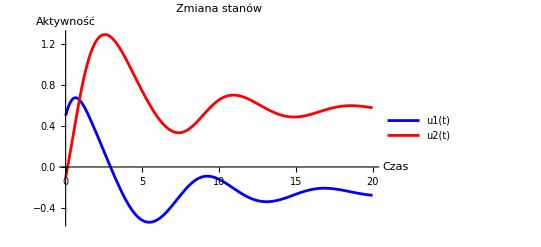

```mathematica
Plot[Evaluate[{u1[t],u2[t]}/. solution],{t,0,20},PlotLegends->{"u1(t)","u2(t)"},PlotStyle->{Blue,Red},PlotLabel->"Zmiana stanów",AxesLabel->{"Czas","Aktywność"}]
```

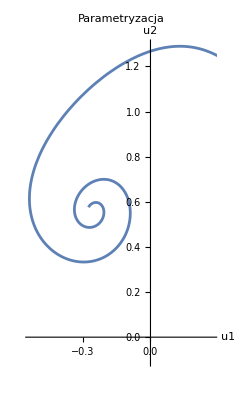

```mathematica
ParametricPlot[Evaluate[{u1[t],u2[t]}/. solution],{t,0,20},AxesLabel->{"u1","u2"},PlotLabel->"Parametryzacja"]
```

Możemy jeszcze rozpatrzyć funkcję energetyczną układu aby sprawdzić czy wraz z biegiem czasu będzie ona dążyć do stabilności.

```mathematica
u1Sol[t_]:=u1[t]/. solution[[1]];
u2Sol[t_]:=u2[t]/. solution[[1]];
```

```mathematica
uSol={u1Sol,u2Sol};
```

```mathematica
En[t_]:=  -1/2 Sum[w[[i,j]] uSol[[i]][t] uSol[[j]][t], {i,1,2}, {j,1,2}] - I0[[1]] u1Sol[t] - I0[[2]] u2Sol[t]
```

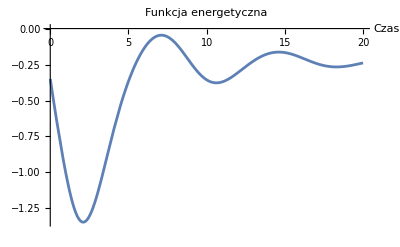

```mathematica
Plot[En[t],{t,0,20},
PlotLabel->"Funkcja energetyczna",AxesLabel->{"Czas"}]
```

Teraz będę analizować stabilność równań różniczkowych opisujących stany naszych neuronów. Najpierw będę przyrównywać równania różniczkowe kolejno u1, u2 do 0 i będę szukać punktów równowagi.

```mathematica
eqns1 =
{-u1+w[[1,1]]activation[u1]+w[[1,2]] activation[u2]+I0[[1]],-u2+w[[2,1]] activation[u1]+w[[2,2]] activation[u2] + I0[[2]]};
jacobian=D[eqns1,{{u1,u2}}];
solution=FindRoot[eqns1,{{u1,0},{u2,0}}];
jacobian1=jacobian/. solution;
Eigenvalues[jacobian1]
```

{-0.158657+0.830152 ⅈ,-0.158657-0.830152 ⅈ}

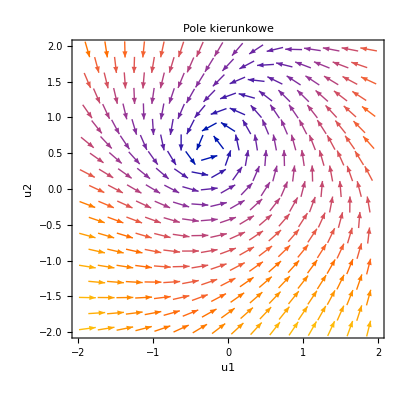

```mathematica
VectorPlot[{eqns1[[1]],eqns1[[2]]},{u1,-2,2},{u2,-2,2},AxesLabel->{"u1","u2"},PlotLabel->"Pole kierunkowe"]
```

Teraz pokażmy przykład, gdzie będzie nie optymalnie zdefiniowana funkcja aktywacji, przez co sieć z czasem nie będzie się stabilizować. Zmienię również macierz wag.

```mathematica
tau=3; 
W={{0,-1/2},{-1/2,0}}; 
I0={0,0}; 
activation1[u_]:=Tanh[u];
```

```mathematica
eqns={tau y1'[t]==-y1[t]+W[[1,1]] activation1[y1[t]]+W[[1,2]] activation1[y2[t]]+I0[[1]],tau y2'[t]==-y2[t]+W[[2,1]] activation1[y1[t]]+W[[2,2]] activation1[y2[t]]+I0[[2]]};
```

```mathematica
initialConditions={y1[0]==0.5,y2[0]==-0.1};
```

```mathematica
solution=NDSolve[{eqns,initialConditions},{y1,y2},{t,0,20}];
```

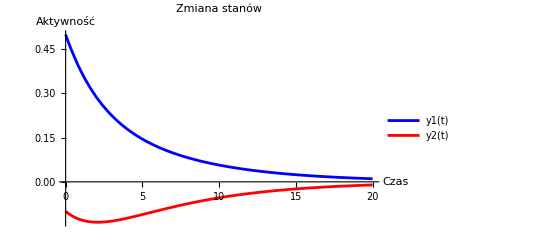

```mathematica
Plot[Evaluate[{y1[t],y2[t]}/. solution],{t,0,20},PlotLegends->{"y1(t)","y2(t)"},PlotStyle->{Blue,Red},
PlotLabel->"Zmiana stanów",AxesLabel->{"Czas","Aktywność"}]
```

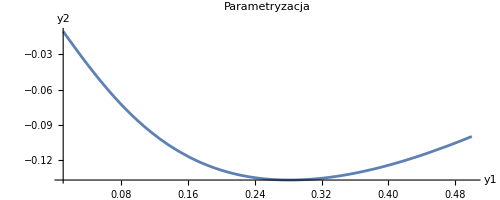

```mathematica
ParametricPlot[Evaluate[{y1[t],y2[t]}/. solution],{t,0,20},AxesLabel->{"y1","y2"},
PlotRange->All,
PlotLabel->"Parametryzacja"]
```

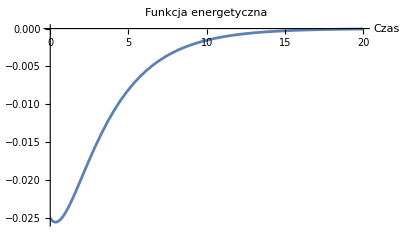

```mathematica
y1Sol[t_]:=y1[t]/. solution[[1]];
y2Sol[t_]:=y2[t]/. solution[[1]];
uSol={y1Sol,y2Sol};
En[t_]:=  -1/2 Sum[W[[i,j]] uSol[[i]][t] uSol[[j]][t], {i,1,2}, {j,1,2}] - I0[[1]] y1Sol[t] - I0[[2]] y2Sol[t];
Plot[En[t],{t,0,20},
PlotLabel->"Funkcja energetyczna",AxesLabel->{"Czas"}]
```

```mathematica
eqns2 =
{-y1+W[[1,1]]activation1[y1]+W[[1,2]] activation1[y2]+I0[[1]],-y2+W[[2,1]] activation1[y1]+W[[2,2]] activation1[y2] + I0[[2]]};
jacobian=D[eqns2,{{y1,y2}}];

solution1=FindRoot[eqns2,{{y1,1},{y2,1}}]
jacobian2=jacobian/. solution1;
Eigenvalues[jacobian1]
```

{y1→0.,y2→0.}

```mathematica
VectorPlot[{eqns1[[1]],eqns1[[2]]},{u1,-2,2},{u2,-2,2},AxesLabel->{"u1","u2"},PlotLabel->"Pole kierunkowe"]
```

-Graphics-

Tutaj sieć złożona z 4 neuronów

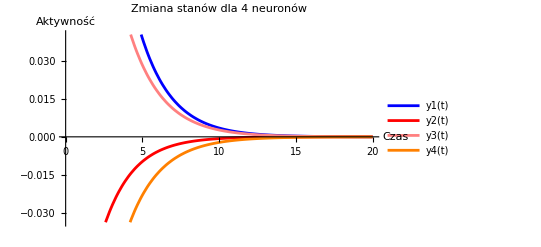

```mathematica
tau=1; 
W={{0,-1/2,1/3,-1/4},{-1/2,0,1/4,-1/3},{1/3,1/4,0,-1/5},{-1/4,-1/3,-1/5,0}};
I0={0,0,0,0}; 
eqns=Table[tau y[i]'[t]==-y[i][t]+Sum[W[[i,j]] activation[y[j][t]],{j,1,4}]+I0[[i]],{i,1,4}];
initialConditions={y[1][0]==0.5,y[2][0]==-0.1,y[3][0]==0.2,y[4][0]==-0.3};
solution=NDSolve[{eqns,initialConditions},Table[y[i],{i,1,4}],{t,0,20}];
Plot[Evaluate[Table[y[i][t],{i,1,4}]/. solution],{t,0,20},PlotLegends->{"y1(t)","y2(t)","y3(t)","y4(t)"},PlotStyle->{Blue,Red,Pink,Orange},PlotLabel->"Zmiana stanów dla 4 neuronów",AxesLabel->{"Czas","Aktywność"}
]
```

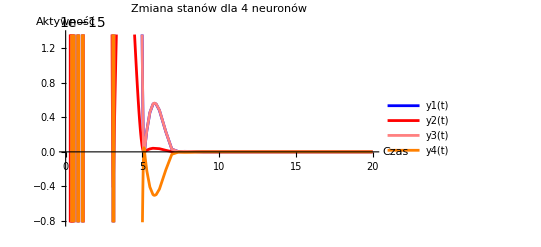

```mathematica
tau=0.01; 
W={{0,-1/2,1/3,-1/4},{-1/2,0,1/4,-1/3},{1/3,1/4,0,-1/5},{-1/4,-1/3,-1/5,0}};
I0={0,0,0,0}; 
eqns=Table[tau y[i]'[t]==-y[i][t]+Sum[W[[i,j]] activation[y[j][t]],{j,1,4}]+I0[[i]],{i,1,4}];
initialConditions={y[1][0]==0.5,y[2][0]==-0.1,y[3][0]==0.2,y[4][0]==-0.3};
solution=NDSolve[{eqns,initialConditions},Table[y[i],{i,1,4}],{t,0,20}];
Plot[Evaluate[Table[y[i][t],{i,1,4}]/. solution],{t,0,20},PlotLegends->{"y1(t)","y2(t)","y3(t)","y4(t)"},PlotStyle->{Blue,Red,Pink,Orange},PlotLabel->"Zmiana stanów dla 4 neuronów",AxesLabel->{"Czas","Aktywność"}
]
```

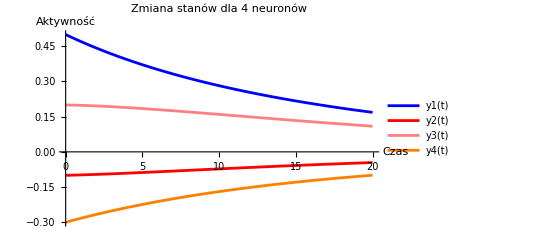

```mathematica
tau=10; 
W={{0,-1/2,1/3,-1/4},{-1/2,0,1/4,-1/3},{1/3,1/4,0,-1/5},{-1/4,-1/3,-1/5,0}};
I0={0,0,0,0}; 
eqns=Table[tau y[i]'[t]==-y[i][t]+Sum[W[[i,j]] activation[y[j][t]],{j,1,4}]+I0[[i]],{i,1,4}];
initialConditions={y[1][0]==0.5,y[2][0]==-0.1,y[3][0]==0.2,y[4][0]==-0.3};
solution=NDSolve[{eqns,initialConditions},Table[y[i],{i,1,4}],{t,0,20}];
Plot[Evaluate[Table[y[i][t],{i,1,4}]/. solution],{t,0,20},PlotLegends->{"y1(t)","y2(t)","y3(t)","y4(t)"},PlotStyle->{Blue,Red,Pink,Orange},PlotLabel->"Zmiana stanów dla 4 neuronów",AxesLabel->{"Czas","Aktywność"}
]
```

## Sieci dyskretne

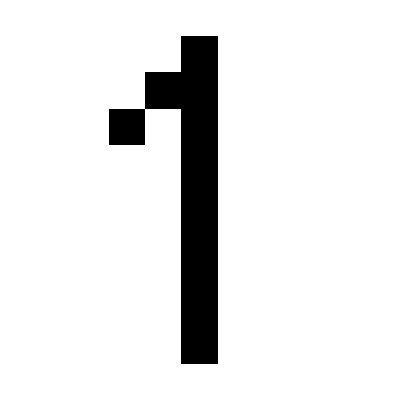

```mathematica
pixel[matrix_]:=Module[{rows,cols,graphics},{rows,cols}=Dimensions[matrix];(*Wymiary macierzy*)graphics=Table[{If[matrix[[i,j]]==1,Black,White],(*Kolor:1->Czarny,0->Biały*)Rectangle[{j-1,rows-i},{j,rows-i-1}] (*Kwadrat odpowiadający elementowi*)},{i,rows},{j,cols}];
Graphics[{EdgeForm[None],graphics},AspectRatio->Automatic]]
one={
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,1,1,-1,-1,-1,-1},
{-1,-1,1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1}
};
pixel[one]
```

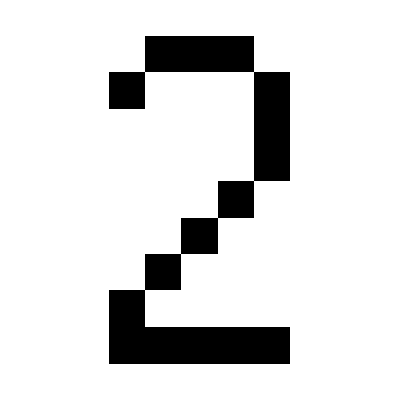

```mathematica
two={
{-1,-1,-1,1,1,1,-1,-1,-1},
{-1,-1,1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,-1,-1,1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,1,-1,-1,-1,-1,-1},
{-1,-1,1,-1,-1,-1,-1,-1,-1},
{-1,-1,1,1,1,1,1,-1,-1}
};
pixel[two]
```

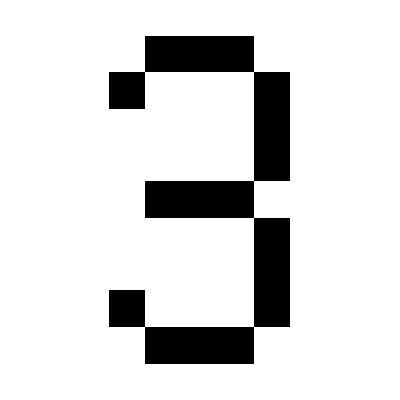

```mathematica
three={
{-1,-1,-1,1,1,1,-1,-1,-1},
{-1,-1,1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,1,1,1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,-1,-1,-1,1,-1,-1},
{-1,-1,1,-1,-1,-1,1,-1,-1},
{-1,-1,-1,1,1,1,-1,-1,-1}
};
pixel[three]
```

Dla ułatwienia z macierzy wzorcowych 9x9 tworzymy listy o 81 elementach. Następnie tworzymy macierz wagową pamiętając, że elementy na przekątnej to 0 (co wynika z własności tej macierzy) i  dla i różnego od j korzystając ze wzoru:
w_ij=1/n∑_(k = 0)^p (a_i^k)_(a_j^k)_                    ,gdzie p to liczba zapamiętywanych wzorców, a a_i^k  i a_j^kto elementy listy k-tego wzorca o indeksach i,j=1,...,81. Otrzymujemy macierz W o wymiarach 81x81.

```mathematica
cyfry={Flatten[one], Flatten[two], Flatten[three]};
W=Table[If[i==j,0,1/81*Sum[cyfry[[k,i]]*cyfry[[k,j]],{k,1,3}]],{i,1,81},{j,1,81}]
```

Nazwiemy naszą zaszumioną macierz wejściową input, następnie dla uproszczenia zamienimy ją na listę o 81 wyrazach. Rozważamy poniższe funkcje dla t=1,...,10, gdzie t oznacza liczbę iteracji oraz tworzymy macierz zerową A o wymiarach 81x10, której kolumny to odpowiednio macierze wyjściowe po (t-1)-szej iteracji.  W pierwszej kolumnie mamy listę wejściową, czyli Flatten[input].
A_i(t+1)= f ( ∑_(j=1)^n w_ijA_j(t) )       oraz        f(y_j(t))=Piecewise[{{1, gdy   ∑_(j=1)^n w_ij A_j(t)>0}, {-1, gdy   ∑_(j=1)^n w_ij A_j(t)<=0}}]

```mathematica
input={
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,1,1,-1,-1,-1,-1},
{-1,-1,1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{1,1,1,1,1,1,-1,1,-1}};
```

```mathematica
f[h_]:=If[h>0,1,-1];
A=ConstantArray[0,{81,10}];

(*Warunki początkowe*)
A[[All,1]]=Flatten[input];

(*Obliczanie iteracyjne A[i,t]*)
For[t=1,t<=9,t++,If[Partition[A[[All,t]],9]==one || Partition[A[[All,t]],9]==two ||Partition[A[[All,t]],9]==three, A[[All,t+1]]=A[[All,t]],For[i=1,i<=81,i++,A[[i,t+1]]=f[Sum[W[[i,j]]*A[[j,t]],{j,1,81}]];];];];
```

Teraz napiszemy funkcje output zależnej od t, która dla naszej macierzy A zwraca zapikselowany obrazek wyjściowej macierzy po t-1 iteracjach.

```mathematica
output[t_]:=pixel[Partition[A[[All,t]],9]]
```

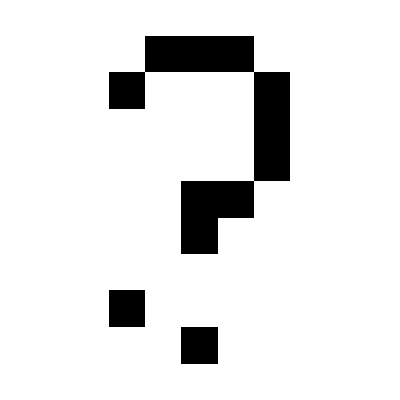

```mathematica
output[2]
```

## Analogiczny kod użyty przy czterech wzorcach

Dodajemy czwarty wzorzec, czyli macierz four.

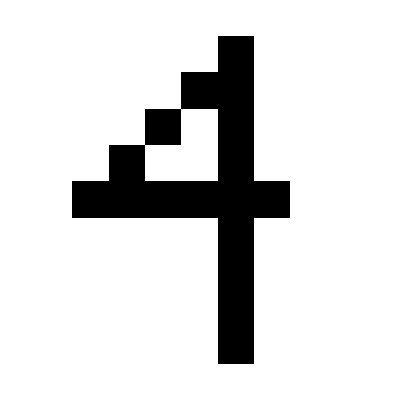

```mathematica
four={
{-1,-1,-1,-1,-1,1,-1,-1,-1},
{-1,-1,-1,-1,1,1,-1,-1,-1},
{-1,-1,-1,1,-1,1,-1,-1,-1},
{-1,-1,1,-1,-1,1,-1,-1,-1},
{-1,1,1,1,1,1,1,-1,-1},
{-1,-1,-1,-1,-1,1,-1,-1,-1},
{-1,-1,-1,-1,-1,1,-1,-1,-1},
{-1,-1,-1,-1,-1,1,-1,-1,-1},
{-1,-1,-1,-1,-1,1,-1,-1,-1}
};
pixel[four]
```

```mathematica
cyfry2={Flatten[one], Flatten[two], Flatten[three],Flatten[four]};
W2=Table[If[i==j,0,1/81*Sum[cyfry2[[k,i]]*cyfry2[[k,j]],{k,1,4}]],{i,1,81},{j,1,81}]
```

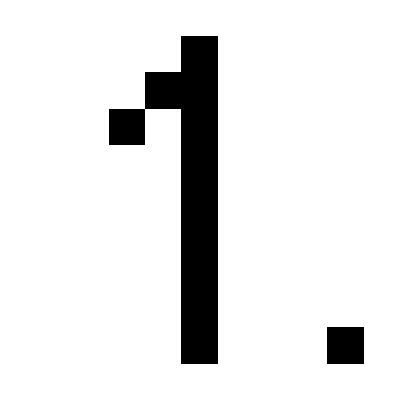

```mathematica
input2={
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,1,1,-1,-1,-1,-1},
{-1,-1,1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,-1},
{-1,-1,-1,-1,1,-1,-1,-1,1}
};
f[h_]:=If[h>0,1,-1];
B=ConstantArray[0,{81,10}];

(*Warunki początkowe*)
B[[All,1]]=Flatten[input2];

(*Obliczanie iteracyjne z[i][t]*)
For[t=1,t<=9,t++,If[Partition[B[[All,t]],9]==one || Partition[B[[All,t]],9]==two ||Partition[B[[All,t]],9]==three ||Partition[B[[All,t]],9]==four, B[[All,t+1]]=B[[All,t]],For[i=1,i<=81,i++,B[[i,t+1]]=f[Sum[W2[[i,j]]*B[[j,t]],{j,1,81}]];];];];
output2[t_]:=pixel[Partition[B[[All,t]],9]]
output2[1]
```

## Analogiczny kod dla kółka i krzyżyka

Nauczymy sieć składającą się z n=9 neuronów dwóch wzorców.

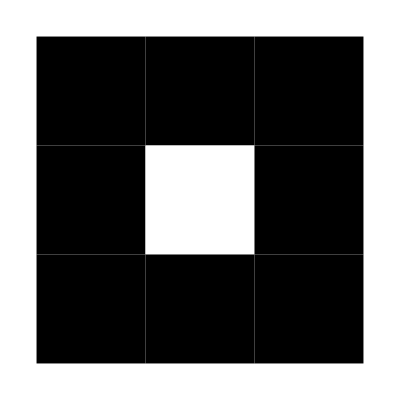

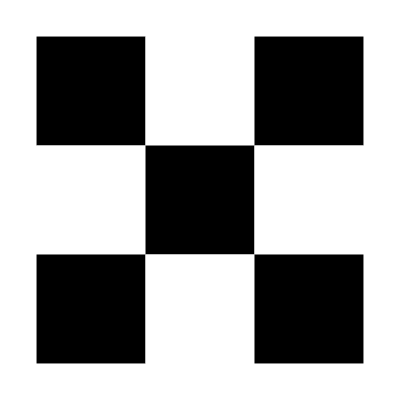

```mathematica
kolko={
{1,1,1},
{1,-1,1},
{1,1,1}};
pixel[kolko]
krzyzyk={
{1,-1,1},
{-1,1,-1},
{1,-1,1}};
pixel[krzyzyk]
wzory={Flatten[kolko], Flatten[krzyzyk]};
W3=Table[If[i==j,0,1/9*Sum[wzory[[k,i]]*wzory[[k,j]],{k,1,2}]],{i,1,9},{j,1,9}];
```

```mathematica
input3={{1,1,1},
{-1,1,1},
{1,1,1}};
f[h_]:=If[h>0,1,-1];
K=ConstantArray[0,{9,10}];
```

```mathematica
K[[All,1]]=Flatten[input3];

For[t=1,t<=9,t++,If[Partition[K[[All,t]],3]==kolko || Partition[K[[All,t]],3]==krzyzyk , K[[All,t+1]]=K[[All,t]],For[i=1,i<=9,i++,K[[i,t+1]]=f[Sum[W3[[i,j]]*K[[j,t]],{j,1,9}]];];];];
```

```mathematica
output3[t_]:=pixel[Partition[K[[All,t]],3]]
```

```mathematica
output3[3]
```

-Graphics-